# InlämingUppgift

## Lucas Larsson

## 1. Uppgift 1

### Show in ℝ^3 the solution set to the following equation Piecewise[{{z≥√(x^2+y^2) x^2+y^2+z^2≤1, }}]

```mathematica
RegionPlot3D[z≥√(x^2+y^2),{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

```mathematica
RegionPlot3D[z≥√(x^2+y^2),{x,-1,1},{y,-1,1},{z,-1,1},PlotTheme->"Detailed"]
```

-Graphics3D-

```mathematica
cone=RegionPlot3D[z≥√(x^2+y^2),{x,-1,1},{y,-1,1},{z,-1,1},PlotTheme->"Detailed",AxesLabel->Automatic,PlotStyle->Red]
```

-Graphics3D-

```mathematica
sphere=RegionPlot3D[x^2+y^2+z^2≤1,{x,-2,2},{y,-2,2},{z,-2,2},PlotTheme->"Detailed",AxesLabel->Automatic,PlotStyle->Blue]
```

-Graphics3D-

```mathematica
RegionPlot3D[x^2+y^2+z^2≤1,{x,-10,10},{y,-10,10},{z,-10,10}]
```

-Graphics3D-

```mathematica
RegionPlot3D[x^2+y^2+z^2≤1,{x,-2,2},{y,-2,2},{z,-2,2},PlotTheme->"Detailed",AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
RegionPlot3D[{z≥√(x^2+y^2),x^2+y^2+z^2≤1},{x,-10,10},{y,-10,10},{z,-10,10},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
RegionPlot3D[{z≥√(x^2+y^2),x^2+y^2+z^2≤1},{x,-10,10},{y,-10,10},{z,-10,10},PlotTheme->"Detailed",AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
RegionPlot3D[{z≥√(x^2+y^2),x^2+y^2+z^2≤1},{x,-1,1},{y,-1,1},{z,-1,1},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
RegionPlot3D[{z≥√(x^2+y^2),x^2+y^2+z^2≤1},{x,-1,1},{y,-1,1},{z,-1,1},PlotTheme->"Detailed",AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Show[cone,sphere]
```

-Graphics3D-

```mathematica
Reduce[ {z≥√(x^2+y^2),x^2+y^2+ z^2≤1},{x,y,z}]
```

(-1/(√2)≤x<0&&((y==-(√(1-2 x^2))/(√2)&&z==√(1-x^2-y^2))||(-(√(1-2 x^2))/(√2)<y<(√(1-2 x^2))/(√2)&&√(x^2+y^2)≤z≤√(1-x^2-y^2))||(y==(√(1-2 x^2))/(√2)&&z==√(1-x^2-y^2))))||(x==0&&((y==-1/(√2)&&z==1/(√2))||(-1/(√2)<y<0&&√(y^2)≤z≤√(1-y^2))||(y==0&&0≤z≤1)||(0<y<1/(√2)&&√(y^2)≤z≤√(1-y^2))||(y==1/(√2)&&z==1/(√2))))||(0<x≤1/(√2)&&((y==-(√(1-2 x^2))/(√2)&&z==√(1-x^2-y^2))||(-(√(1-2 x^2))/(√2)<y<(√(1-2 x^2))/(√2)&&√(x^2+y^2)≤z≤√(1-x^2-y^2))||(y==(√(1-2 x^2))/(√2)&&z==√(1-x^2-y^2))))

```mathematica
(-1/(√2)≤x<0&&((y==-(√(1-2 x^2))/(√2)&&z==√(1-x^2-y^2))||(-(√(1-2 x^2))/(√2)<y<(√(1-2 x^2))/(√2)&&√(x^2+y^2)≤z≤√(1-x^2-y^2))||(y==(√(1-2 x^2))/(√2)&&z==√(1-x^2-y^2))))||(x==0&&((y==-1/(√2)&&z==1/(√2))||(-1/(√2)<y<0&&√(y^2)≤z≤√(1-y^2))||(y==0&&0≤z≤1)||(0<y<1/(√2)&&√(y^2)≤z≤√(1-y^2))||(y==1/(√2)&&z==1/(√2))))||(0<x≤1/(√2)&&((y==-(√(1-2 x^2))/(√2)&&z==√(1-x^2-y^2))||(-(√(1-2 x^2))/(√2)<y<(√(1-2 x^2))/(√2)&&√(x^2+y^2)≤z≤√(1-x^2-y^2))||(y==(√(1-2 x^2))/(√2)&&z==√(1-x^2-y^2))))
```

```mathematica
mars={(-1/(√2)≤x<0&&((y==-(√(1-2 x^2))/(√2)&&z==√(1-x^2-y^2))||(-(√(1-2 x^2))/(√2)<y<(√(1-2 x^2))/(√2)&&√(x^2+y^2)≤z≤√(1-x^2-y^2))||(y==(√(1-2 x^2))/(√2)&&z==√(1-x^2-y^2))))||(x==0&&((y==-1/(√2)&&z==1/(√2))||(-1/(√2)<y<0&&√(y^2)≤z≤√(1-y^2))||(y==0&&0≤z≤1)||(0<y<1/(√2)&&√(y^2)≤z≤√(1-y^2))||(y==1/(√2)&&z==1/(√2))))||(0<x≤1/(√2)&&((y==-(√(1-2 x^2))/(√2)&&z==√(1-x^2-y^2))||(-(√(1-2 x^2))/(√2)<y<(√(1-2 x^2))/(√2)&&√(x^2+y^2)≤z≤√(1-x^2-y^2))||(y==(√(1-2 x^2))/(√2)&&z==√(1-x^2-y^2))))}
```

{(-1/(√2)≤x<0&&((y==-(√(1-2 x^2))/(√2)&&z==√(1-x^2-y^2))||(-(√(1-2 x^2))/(√2)<y<(√(1-2 x^2))/(√2)&&√(x^2+y^2)≤z≤√(1-x^2-y^2))||(y==(√(1-2 x^2))/(√2)&&z==√(1-x^2-y^2))))||(x==0&&((y==-1/(√2)&&z==1/(√2))||(-1/(√2)<y<0&&√(y^2)≤z≤√(1-y^2))||(y==0&&0≤z≤1)||(0<y<1/(√2)&&√(y^2)≤z≤√(1-y^2))||(y==1/(√2)&&z==1/(√2))))||(0<x≤1/(√2)&&((y==-(√(1-2 x^2))/(√2)&&z==√(1-x^2-y^2))||(-(√(1-2 x^2))/(√2)<y<(√(1-2 x^2))/(√2)&&√(x^2+y^2)≤z≤√(1-x^2-y^2))||(y==(√(1-2 x^2))/(√2)&&z==√(1-x^2-y^2))))}

```mathematica
ContourPlot3D[ {z≥√(x^2+y^2)},{X,-10,10},{Y,-10,10},{z,-10,10}]
```

## 2. Uppgift 1

### Calculate the Angel θ between the two vectors b and a a =2i-2j-2k b=3i-2j-k

```mathematica
a = {2,-2,-2};
```

```mathematica
b= {3,-2,-1};
```

```mathematica
ArcCos[(a.b)/(Norm[a]*Norm[b])]
```

ArcCos[√(6/7)]

```mathematica
With[{d=N[ArcCos[√(6/7)]/°]},Defer[d °]]
```

22.2077 °

```mathematica
DMSList[N[ArcCos[√(6/7)]/°]]
```

{22,12,27.5555}

```mathematica
N[ArcCos[√(6/7)]/°]
```

22.2077

```mathematica
N[ArcCos[√(6/7)]]
```

0.387597

```mathematica
π Rationalize[N[ArcCos[√(6/7)]]/π]
```

0.387597

```mathematica
With[{d=N[ArcCos[√(6/7)]/°]},Defer[d °]]
```

22.2077 °

```mathematica
π/2-ArcCos[√(6/7)]
```

π/2-ArcCos[√(6/7)]

```mathematica
N[ArcCos[√(6/7)]/°]
```

22.2077

```mathematica
ScientificForm[22.207654298596495]
```

2.22077×10^1

```mathematica
(a.b)/Norm[a] *1/Norm[b]
```

√(6/7)

```mathematica
ArcCos[(a.b)/(Norm[a]*Norm[b])]
```

ArcCos[√(6/7)]

```mathematica
ArcCos[√(6/7)]
```

## 3. Uppgift 3

```mathematica
Solve [x^2=16,x]
```

Set::write: Tag Power in 10.^2 is Protected.

Solve::ivar: 10. is not a valid variable.

Solve[16,10.]

```mathematica
Solve[{x+2y+3z ==1,
      2x+4y+7z==2, 
      3x+7y+11z==8},{x,y,z}]
```

Solve::ivar: 10. is not a valid variable.

Solve[{False,False,False},{10.,10.,10.}]

```mathematica
Plot3D[x+2y+3z=1,{x,-10,10},{y,-10,10},AxesLabel->{x,y,z}]
```

Set::write: Tag Plus in -19.9971-9.99857+30. is Protected.

-Graphics3D-

```mathematica
functionA =ContourPlot3D[x+2y+3z==1,{x,-100,100},{y,-100,100},{z,-100,100},ContourStyle-> Green,AxesLabel->Automatic]
```

```mathematica
Plot3D[x+2y-1==-3z,{x,-1000,1000},{y,-1000,1000},AxesLabel->{"x","y","z"},PlotRange->{-1000,1000}]
```

-Graphics3D-

```mathematica
functionB=ContourPlot3D[2x+4y+7z==2,{x,-100,100},{y,-100,100},{z,-100,100},Contours-> 3,ContourStyle-> Blue]
```

-Graphics3D-

```mathematica
functionC=ContourPlot3D[3x+7y+11z==8,{x,-100,100},{y,-100,100},{z,-100,100},Contours->3,ContourStyle->Yellow]
```

-Graphics3D-

```mathematica
Show[functionA,functionB,functionC]
```

-Graphics3D-

```mathematica
Rasterize[%69,"Image"]
```

```mathematica
Show[%69,Boxed->False]
```

-Graphics3D-

```mathematica
RegionPlot3D[x+2y+3z<1,{x,-100,100},{y,-100,100},{z,-100,100}]
```

-Graphics3D-

RegionPlot3D[x+2 y+3 z==1,2 x+4 y+7 z==2,{x,-100,100},{y,-100,100},{z,-100,100}]

-Graphics3D-

## 4. Uppgift 1

```mathematica
place holder
```

## 5. Uppgift 1

### Show that the following equation does not have solutions in ℝ^2 Piecewise[{{3x+4y-z=8 6x+8y-2z=3, }}]

```mathematica
Reduce[{3x+4y-z==8,6x+8y-2z==3},{x,y,z}]
```

False

Set::write: Tag Plus in -29.9988+4 y-z is Protected.

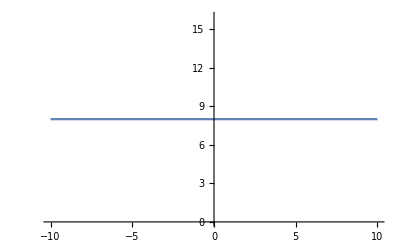

```mathematica
function1 =Plot[3x+4y-z=8, {x,-10,10}]
```

Set::write: Tag Plus in -59.9975+8 y-z is Protected.

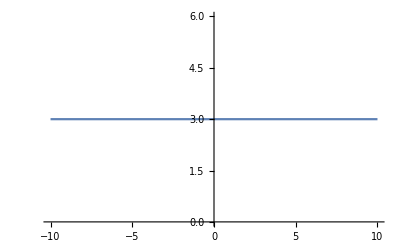

```mathematica
function2 =Plot[6x+8y-z=3, {x,-10,10}]
```

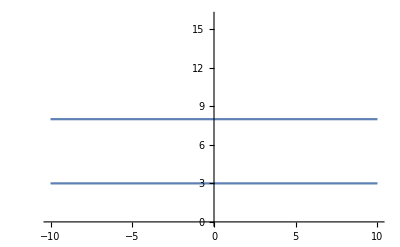

```mathematica
Show[function1,function2]
```

```mathematica
fun1  =Plot3D[3 x+4 y-z=8,{x,7,9},{y,7,9},PlotTheme->"Detailed",AxesLabel->{x,y,z},PlotStyle->Red]
```

-Graphics3D-

```mathematica
fun2 =Plot3D[6 x+8y-2z=3,{x,-10,10},{y,-10,10},PlotTheme->"Detailed",AxesLabel->{x,y,z},PlotStyle->Blue]
```

Set::write: Tag Plus in -79.9886-59.9914-2 z is Protected.

-Graphics3D-

```mathematica
Show[fun1,fun2]
```

-Graphics3D-

```mathematica
ContourPlot3D[3x+4y-z==8, {x,-10,10},{y,-10,10},{z,-10,10}]
```

-Graphics3D-

## 6. Uppgift 1

```mathematica
place holder
```

## 7. Uppgift 1

```mathematica
place holder
```

## 8. Uppgift 1

```mathematica
place holder
```

## 9. Uppgift 1

```mathematica
place holder
```

## 10. Uppgift 1

```mathematica
dsf
```